## The vibrational band in the odd-A 63Cu nucleus

The band is formed via the particle+rotor coupling.
The odd-proton from p(3/2) orbital is coupling with the I=2 vibrational phonon level of its even-core “partner”

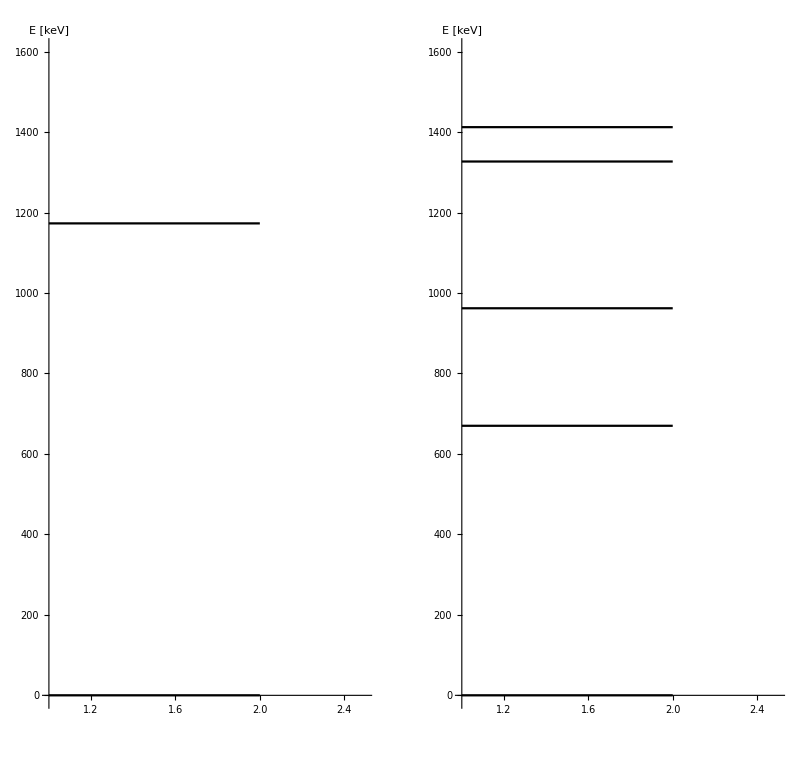

```mathematica
usedenergies63Cu={1412.16,1326.76,962.02,669.93,0.0};
usedenergies62Ni={1172.98,0.0};
energyPlot[data_]:=Plot[data,{x,1,2},Axes->{False,True},PlotRange->{{1,2.5},{0,1600}},AspectRatio->2,AxesStyle->Directive[Black,Thick],AxesLabel->{None,"E [keV]"},LabelStyle->{18,Bold,Black,FontFamily->"Arial"},PlotStyle->Black];
p1=energyPlot[usedenergies63Cu];
p2=energyPlot[usedenergies62Ni];
GraphicsGrid[{{p2,p1}}]
```